# Outage-Capacity Bound

## Negative Exponential Distribution X_i~exp(-1)

## Basic Calculations

## First Steps

```mathematica
ClearAll[a, n, c, x, f, F, G, H, T, L, R, Phi, Psi, cmin]
f[x_]:=Exp[x]
F[x_] := Exp[x]
G[x_] := Log[x]
```

```mathematica
H[x_, n_, a_]:= (n-1)*G[1-(n-1)x]+G[a+x]
```

```mathematica
T[x_, n_, a_]:=Integrate[H[x, n, a], x]
T[x, n, a]
```

-n x+(a+x) Log[a+x]+(-1+(-1+n) x) Log[1+x-n x]

```mathematica
T[x_, n_, a_]:=-n x+(a+x) Log[a+x]+(-1+(-1+n) x) Log[1+x-n x]
T[x, n, a]
```

-n x+(a+x) Log[a+x]+(-1+(-1+n) x) Log[1+x-n x]

### Left Hand/Right Hand Sides

```mathematica
Simplify[T[(1-a)/n, n, a] - T[c, n, a]]
```

-1+a+c n-(a+c) Log[a+c]+(1+c-c n) Log[1+c-c n]

```mathematica
L[c_, n_, a_]:=-1+a+c n-(a+c) Log[a+c]+(1+c-c n) Log[1+c-c n]
```

```mathematica
R[c_, n_, a_]:= ((1-a)/n-c)H[c, n, a]
```

```mathematica
R[c, n, a]
```

(-c+(1-a)/n) (Log[a+c]+(-1+n) Log[1-c (-1+n)])

```mathematica
(*Simplify[L[c, n, a]≤R[c, n, a],c]*)
Simplify[-1+a+c n-(a+c) Log[a+c]+(1+c-c n) Log[1+c-c n] ≤ (-c+(1-a)/n) (Log[a+c]+(-1+n) Log[1-c (-1+n)])]
```

(n (-1+a+c n)+(-1+a-a n) Log[a+c]+(1+a (-1+n)) Log[1+c-c n])/n≤0

### Determine c_min

```mathematica
(*Reduce[L[c, n, a]≤R[c, n, a],c]*)
Reduce[L[c, 3, 0]≤R[c, 3, 0],c]
```

Root0.0945Root[{-3+Log[1-2 #1]-Log[#1]+9 #1&,0.094541577788104161991}]0.09454157778810417≤c<1/2

```mathematica
cmin[n_, a_] := TakeLargest[{N[Reduce[L[c, n, a]≤R[c, n, a],c][[1]]], 0}, 1][[1]]
cmin[3, 0]
```

0.0945416

```mathematica
Manipulate[Reduce[L[c, 3, a]≤R[c, 3, a],c], {a, 0, 1, Appearance->"Labeled"}, ContinuousAction->False] (*Different a*)
```

```mathematica
Manipulate[Reduce[L[c, n, 0]≤R[c, n, 0],c], {n, 2, 10, Appearance->"Labeled", Integer}] (*Different n*)
```

```mathematica
Manipulate[Reduce[L[c, n, a]≤R[c, n, a],c], {n, 2, 10, Appearance->"Labeled", Integer}, {a, 0, 1, Appearance->"Labeled"}, ContinuousAction->False]
```

## Plots for Illustration

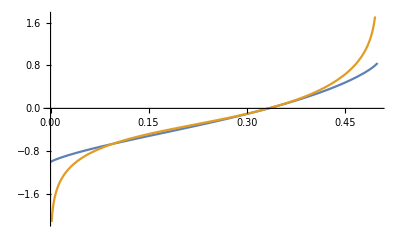

```mathematica
Plot[{L[c, 3, 0],R[c, 3, 0]},{c,0,1/2}]
```

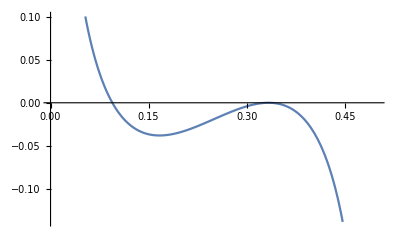

```mathematica
Plot[L[c, 3, 0]-R[c, 3, 0],{c,0,1/2}]
```

```mathematica
Manipulate[Plot[L[c, 3, a]-R[c, 3, a],{c,0,1/2}],{a,0,1,Appearance->"Labeled"}]
```

## Calculation of Bounds

## Function ϕ

For a increasing density the function ϕ is defined according to (3.9) as follows:
	ϕ = Piecewise[{{H(0), if c(a)>0}, {nψ(a), if c(a)=0}}]
with ψ(t)=E[X | X>=G(t)]

```mathematica
Psi[a_] := 1/(1-a)*Integrate[x*f[x],{x,G[a], 0}]
Psi[a_] := (-1+a-a Log[a])/(1-a)
```

```mathematica
Phi[a_, n_] := Piecewise[{{H[0, n, a], cmin[n, a]>0}, {n*Psi[a], cmin[n, a]==0}}]
```

```mathematica
N[Phi[.1, 3]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-2.30259

### Plots

```mathematica
Manipulate[Plot[{H[0, n, a], n*Psi[a]},{a,0,1},PlotLegends->{"H(0)", "nψ"}], {n, 3, 10, Appearance->"Labeled", Integer}]
```